#### Cost Function for a Linear Propagator Model

1+π Cos[π t]+3.14159 Cos[2 π t]

1+2 π Cos[2 π t]

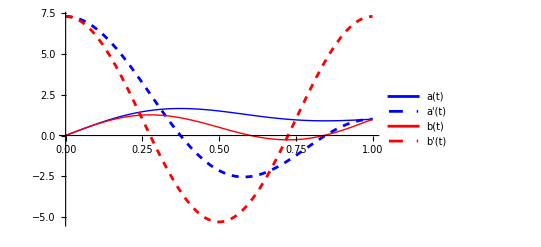

P(t) = 0.6-3.36356 ⅇ^(-10 t)+0.285938 Cos[π t]+2.47762 Cos[2 π t]+0.0898302 Sin[π t]+1.55674 Sin[2 π t]

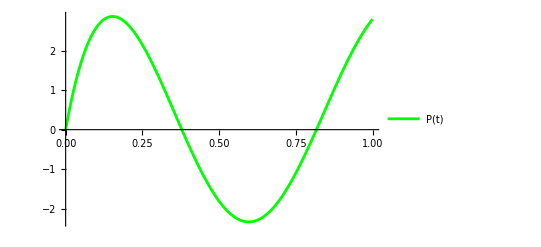

```mathematica
ClearAll["Global`*"]
(*Define the input functions and parameters*)
an ={1, 0.5};  
bn = {0, 1};
a[t_]:= t + an[[1]]  Sin[Pi  t] + an[[2]] Sin[2 Pi t];(*Define a(t) here*)
b[t_]:=t +  bn[[1]]  Sin[Pi  t] + bn[[2]] Sin[2 Pi t];(*Define b(t) here*)
lambda= 5(*Define lambda here*);
rho= 10 (*Define rho here*);

(*Define derivatives of a(t) and b(t)*)
aPrime[t_]=D[a[t],t]
bPrime[t_]=D[b[t],t]

(*Plot a(t),a'(t),b(t),b'(t) for t in[0,1]*)Plot[{a[t],aPrime[t],b[t],bPrime[t]},{t,0,1},PlotStyle->{{Thick,Blue},{Dashed,Blue},{Thick,Red},{Dashed,Red}},PlotLegends->{"a(t)","a'(t)","b(t)","b'(t)"}]

(*Derive P(t) analytically*)P[t_ ]=Integrate[Exp[-rho (t-s)] (aPrime[s]+lambda bPrime[s]),{s,0,t},Assumptions->{t>=0,rho>0}];

(*Print the analytical formula for P(t)*)
PFormula=P[t]//Simplify;
Print["P(t) = ",PFormula]
(* Plot P(t)*)
Plot[P[t], {t, 0,1},
PlotStyle->{Green}, 
PlotLegends->{"P(t)"}]
```

```mathematica
(*Derive the value L(a), L(b)*)
La=Integrate[aPrime[t]*P[t],{t,0,1}];
Lb=Integrate[bPrime[t] lambda *P[t],{t,0,1}];

(*Numeric value of L*)
LaNumeric=N[La];
LbNumeric=N[Lb];

(*Output the results*)
Print["L(a) : ",{La,Chop[LaNumeric]}]
Print["L(b) : ",{Lb,Chop[LbNumeric]}]
```

L(a) : {4.95822+3.0339×10^-16 ⅈ,4.95822}

L(b) : {32.3481,32.3481}